```mathematica
<<MASStoolbox`
<<MASStoolbox`Style`
```

### PFK (custom mechanism like book)

```mathematica
SetDirectory[NotebookDirectory[]];
iABglycolysis=Import["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
pfkRxn=Cases[getReactions@rbc,r_reaction/;getID[r]==="PFK"][[1]]
```

(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK

```mathematica
pfkModule=constructEnzymeModule[pfkRxn,Mechanism->{"E"->"EA","EA"->"EAB","EAB"->"EPQR","EPQR"->"E"},Inhibitors->{m["amp","c"]},Activators->{m["atp","c"]},ActivationSites->4,InhibitionSites->4];
```

```mathematica
subsetRxns=Cases[pfkModule["Fluxes"],s_String/;StringMatchQ[s,RegularExpression[".*Catalysis.*"]]];
catalysisModule=deleteReactions[#,Complement[#["Fluxes"],subsetRxns]]&[pfkModule];
pos=Position[catalysisModule["Species"],e_enzyme/;Length[getCatalytic[e]]>0][[All,1]];
ssEqu=Thread[Equal[0,catalysisModule.unifyRateConstants[makeRates[catalysisModule]]/.elem_[t]:>elem]][[pos]] ;

vars=catalysisModule["Species"][[pos]];
Print["Solving SS"];
ssSol=Simplify[Solve[ssEqu,vars][[1]]];
```

Solving SS

```mathematica
subsetRxns=Cases[pfkModule["Fluxes"],s_String/;StringMatchQ[s,RegularExpression[".*Inhibition.*"]]];
If[subsetRxns==={},
inhibEqEqu={};,
inhibitionModule=deleteReactions[#,Complement[#["Fluxes"],subsetRxns]]&[pfkModule];
inhibEqEqu=Thread[Equal[0,correctRatesForBindingSites[unifyRateConstants[makeRates[inhibitionModule]]]]];
];

subsetRxns=Cases[pfkModule["Fluxes"],s_String/;StringMatchQ[s,RegularExpression[".*Activation.*"]]];
If[subsetRxns==={},
activEqEqu={};,
activationModule=deleteReactions[#,Complement[#["Fluxes"],subsetRxns]]&[pfkModule];
activEqEqu=Thread[Equal[0,correctRatesForBindingSites[unifyRateConstants[makeRates[activationModule]]]]];
];

transitionStep={0==If[#=!={},#[[1]],{}]&[subRevRateConstsByKeq@Select[unifyRateConstants[makeRates[pfkModule]],MemberQ[#,rateconst[s_String/;StringMatchQ[s,RegularExpression[".*TransitionStep.*"]],_],∞]&]]};
enzForms=Union@Cases[pfkModule["Species"],e_enzyme,∞];
eTotEqu={0==param["PFKtot"]-Plus@@enzForms};

Print["Solving Rest"];
AbsoluteTiming[result=Solve[Join[Equal@@@ssSol,inhibEqEqu,activEqEqu,transitionStep,eTotEqu]//.elem_[t]:>elem,enzForms][[1]];]
Print["Simplifying the result"];
AbsoluteTiming[result=Simplify[result];]
```

Solving Rest

{2.86453,Null}

Simplifying the result

{4.030122,Null}

```mathematica
ssEnzymeLevels[[1,1]]
```

(PFK_R^c)_^→(K_(PFK_R_Catalysis_Release(EPQR->E)) PFKtot_Global (k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶))))/(adp^c (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) fdp^c h^c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ ((K_(PFK_R_Catalysis_Bind(E->EA)) (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c) k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶) k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶)))+K_(PFK_R_Catalysis_Release(EPQR->E)) ((K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) (1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c))) k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) (K_(PFK_R_Catalysis_Bind(EA->EAB)) (K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c) (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) (1+K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) f6p^c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(E->EA))^⟶ ((K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) (1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c))) k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶)))))

```mathematica
result[[1]]
```

(PFK_R^c)_^→(K_(PFK_R_Catalysis_Release(EPQR->E)) (k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶))) {K_EX_adp_c→1,K_EX_atp_c→1,K_EX_f6p_c→1,K_EX_fdp_c→1,K_EX_h_c→1,K_(PFK_R_Catalysis_Bind(EA->EAB))→10.,K_(PFK_R_Catalysis_Bind(E->EA))→14.7059,K_(PFK_R_Catalysis_Release(EPQR->E))→100000,K_(PFK_R_Catalysis_Transition(EAB->EPQR))→100000,Volume_c→1,PFKtot_Global→0.000033}[PFKtot])/(adp^c (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) fdp^c h^c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ ((K_(PFK_R_Catalysis_Bind(E->EA)) (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c) k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶) k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶)))+K_(PFK_R_Catalysis_Release(EPQR->E)) ((K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) (1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c))) k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) (K_(PFK_R_Catalysis_Bind(EA->EAB)) (K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c) (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) (1+K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) f6p^c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(E->EA))^⟶ ((K_PFK_TransitionStep (1+4 K_PFK_Inhibition_amp amp^c+12 K_PFK_Inhibition_amp^2 (amp^c)^2+24 K_PFK_Inhibition_amp^3 (amp^c)^3+24 K_PFK_Inhibition_amp^4 (amp^c)^4)+(1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) (1+K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c))) k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) atp^c (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶)))))

```mathematica
pfkModule
```

```mathematica
adjustedRates=(correctRatesForBindingSites@unifyRateConstants@pfkModule["Rates"])//.elem_[t]:>elem;
```

```mathematica
ssEqu=Thread[0==FilterRules[Thread[pfkModule["Species"]->pfkModule.adjustedRates],_enzyme][[All,2]]];
```

```mathematica
eqEqu=Thread[0=={(-((PFK_R^c)_^(atp^c))/Underscript[K, PFK_Activation_atp]+4 (PFK_R^c)_^ atp^c) Underscript[Volume, c] Subscript[k, PFK_Activation_atp]^⟶,(-((PFK_R^c)_^(atp^c atp^c))/Underscript[K, PFK_Activation_atp]+3 (PFK_R^c)_^(atp^c) atp^c) Underscript[Volume, c] Subscript[k, PFK_Activation_atp]^⟶,(-((PFK_R^c)_^(atp^c atp^c atp^c))/Underscript[K, PFK_Activation_atp]+2 (PFK_R^c)_^(atp^c atp^c) atp^c) Underscript[Volume, c] Subscript[k, PFK_Activation_atp]^⟶,(-((PFK_R^c)_^(atp^c atp^c atp^c atp^c))/Underscript[K, PFK_Activation_atp]+(PFK_R^c)_^(atp^c atp^c atp^c) atp^c) Underscript[Volume, c] Subscript[k, PFK_Activation_atp]^⟶,(-((PFK_T^c)_(amp^c)^)/Underscript[K, PFK_Inhibition_amp]+4 (PFK_T^c)_^ amp^c) Underscript[Volume, c] Subscript[k, PFK_Inhibition_amp]^⟶,(-((PFK_T^c)_(amp^c amp^c)^)/Underscript[K, PFK_Inhibition_amp]+3 (PFK_T^c)_(amp^c)^ amp^c) Underscript[Volume, c] Subscript[k, PFK_Inhibition_amp]^⟶,(-((PFK_T^c)_(amp^c amp^c amp^c)^)/Underscript[K, PFK_Inhibition_amp]+2 (PFK_T^c)_(amp^c amp^c)^ amp^c) Underscript[Volume, c] Subscript[k, PFK_Inhibition_amp]^⟶,(-((PFK_T^c)_(amp^c amp^c amp^c amp^c)^)/Underscript[K, PFK_Inhibition_amp]+(PFK_T^c)_(amp^c amp^c amp^c)^ amp^c) Underscript[Volume, c] Subscript[k, PFK_Inhibition_amp]^⟶,((PFK_R^c)_^-((PFK_T^c)_^)/Underscript[K, PFK_TransitionStep]) Underscript[Volume, c] Subscript[k, PFK_TransitionStep]^⟶}];
```

```mathematica
ssEnzymeLevels=Simplify[Solve[Join[ssEqu,{parameter["PFKtot"]==Total[pfkModule["Enzymes"]]},eqEqu],pfkModule["Enzymes"]]];
```

```mathematica
ssEnzymeLevels[[1,1]]//Short
```

(PFK_R^c)_^→(K_(PFK_R_Catalysis_Release(EPQR->E)) PFKtot_Global (k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶))))/(adp^c (1+4 K_PFK_Activation_atp atp^c+12 K_PFK_Activation_atp^2 (atp^c)^2+24 K_PFK_Activation_atp^3 (atp^c)^3+24 K_PFK_Activation_atp^4 (atp^c)^4) fdp^c h^c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶ ((K_(PFK_R_Catalysis_Bind(E->EA)) (1+K_(PFK_R_Catalysis_Bind(EA->EAB)) f6p^c) k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶) k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+K_(PFK_R_Catalysis_Transition(EAB->EPQR)) (K_(PFK_R_Catalysis_Bind(EA->EAB)) k_(PFK_R_Catalysis_Bind(E->EA))^⟶ k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶+k_(PFK_R_Catalysis_Bind(EA->EAB))^⟶ (k_(PFK_R_Catalysis_Bind(E->EA))^⟶+K_(PFK_R_Catalysis_Bind(EA->EAB)) K_(PFK_R_Catalysis_Bind(E->EA)) f6p^c k_(PFK_R_Catalysis_Transition(EAB->EPQR))^⟶)))+K_(PFK_R_Catalysis_Release(EPQR->E)) («1»+«1» «1»))

```mathematica
ic=#->RandomReal[{0,10}]&/@pfkModule["Species"];
rndParam=updateRules[#->RandomReal[{0,1000}]&/@Union[Cases[pfkModule["Rates"],$MASS$parametersPattern,∞]],{parameter["Volume","c"]->1,m[_,"Xt"]->1}];
{concSol,fluxSol}=simulate[pfkModule,{t,0,1*^18},InitialConditions->ic,Parameters->rndParam];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 4.03362×10^15.

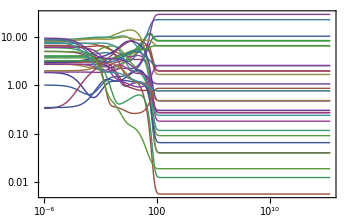

```mathematica
plotSimulation[concSol]
```

```mathematica
pfkTot=MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.ic
MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.concSol/.t->1*^5
```

PFKtot_Global→99.6652

PFKtot_Global→99.6652

```mathematica
Sort[Chop[unifyRateConstants[fluxSol/.t->1*^13]],#[[2]]<#2[[2]]&]
```

{EX_f6p_c→-0.0504008,EX_atp_c→-0.0504008,PFK_TransitionStep→0,PFK_Inhibition_amp→0,PFK_Inhibition_amp→0,PFK_Inhibition_amp→0,PFK_Inhibition_amp→0,PFK_Activation_atp→0,PFK_Activation_atp→0,PFK_Activation_atp→0,PFK_Activation_atp→0,PFK_R_Catalysis_Release(EPQR->E)→0.00055758,PFK_R_Catalysis_Transition(EAB->EPQR)→0.00055758,PFK_R_Catalysis_Bind(EA->EAB)→0.00055758,PFK_R_Catalysis_Bind(E->EA)→0.00055758,PFK_R_Catalysis_Release(EPQR->E)→0.00155324,PFK_R_Catalysis_Transition(EAB->EPQR)→0.00155324,PFK_R_Catalysis_Bind(EA->EAB)→0.00155324,PFK_R_Catalysis_Bind(E->EA)→0.00155324,PFK_R_Catalysis_Release(EPQR->E)→0.0105862,PFK_R_Catalysis_Transition(EAB->EPQR)→0.0105862,PFK_R_Catalysis_Bind(EA->EAB)→0.0105862,PFK_R_Catalysis_Bind(E->EA)→0.0105862,PFK_R_Catalysis_Release(EPQR->E)→0.0183052,PFK_R_Catalysis_Transition(EAB->EPQR)→0.0183052,PFK_R_Catalysis_Bind(EA->EAB)→0.0183052,PFK_R_Catalysis_Bind(E->EA)→0.0183052,PFK_R_Catalysis_Release(EPQR->E)→0.0193986,PFK_R_Catalysis_Transition(EAB->EPQR)→0.0193986,PFK_R_Catalysis_Bind(EA->EAB)→0.0193986,PFK_R_Catalysis_Bind(E->EA)→0.0193986,EX_h_c→0.0504008,EX_fdp_c→0.0504008,EX_adp_c→0.0504008}

```mathematica
ssSimulConc=concSol/.t->1*^13;
```

```mathematica
FilterRules[concSol/.t->1*^13,_enzyme]
(#[[1]]->(#[[2]]/.unifyRateConstants[rndParam]/.ssSimulConc)&/@ssEnzymeLevels[[1]]/.elem_[t]:>elem)/.(MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.ic)
```

{(PFK_R^c)_^→0.147752,(PFK_R^c)_^(atp^c)→0.162715,(PFK_R^c)_^(atp^catp^c)→0.0281926,(PFK_R^c)_^(atp^catp^catp^c)→0.0151793,(PFK_R^c)_^(atp^catp^catp^catp^c)→0.0153247,(PFK_R^c&atp^c)_^→0.0181899,(PFK_R^c&atp^c)_^(atp^c)→0.115075,(PFK_R^c&atp^c)_^(atp^catp^c)→0.00609047,(PFK_R^c&atp^c)_^(atp^catp^catp^c)→0.00454769,(PFK_R^c&atp^c)_^(atp^catp^catp^catp^c)→0.0124021,(PFK_R^c&atp^c&f6p^c)_^→0.000243411,(PFK_R^c&atp^c&f6p^c)_^(atp^c)→0.0000417332,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^c)→2.72685×10^-6,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^c)→0.0000420005,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^catp^c)→0.0000109594,(PFK_R^c&adp^c&fdp^c&h^c)_^→0.0000620707,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)→0.0000575226,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^c)→8.30519×10^-7,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)→0.0000189202,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)→2.39701×10^-6,(PFK_T^c)_^→75.7849,(PFK_T^c)_(amp^c)^→16.5731,(PFK_T^c)_(amp^camp^c)^→5.30873,(PFK_T^c)_(amp^camp^camp^c)^→1.39776,(PFK_T^c)_(amp^camp^camp^camp^c)^→0.0747434}

{(PFK_R^c)_^→0.0659557,(PFK_R^c)_^(atp^c)→0.29054,(PFK_R^c)_^(atp^catp^c)→0.95989,(PFK_R^c)_^(atp^catp^catp^c)→2.1142,(PFK_R^c)_^(atp^catp^catp^catp^c)→2.3283,(PFK_R^c&atp^c)_^→0.0081199,(PFK_R^c&atp^c)_^(atp^c)→0.0357688,(PFK_R^c&atp^c)_^(atp^catp^c)→0.118173,(PFK_R^c&atp^c)_^(atp^catp^catp^c)→0.260282,(PFK_R^c&atp^c)_^(atp^catp^catp^catp^c)→0.286641,(PFK_R^c&atp^c&f6p^c)_^→0.000108658,(PFK_R^c&atp^c&f6p^c)_^(atp^c)→0.000478646,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^c)→0.00158136,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^c)→0.003483,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^catp^c)→0.00383573,(PFK_R^c&adp^c&fdp^c&h^c)_^→0.0000277081,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)→0.000122056,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^c)→0.000403252,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)→0.000888178,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)→0.000978124,(PFK_T^c)_^→33.8301,(PFK_T^c)_(amp^c)^→29.5926,(PFK_T^c)_(amp^camp^c)^→19.4145,(PFK_T^c)_(amp^camp^camp^c)^→8.49134,(PFK_T^c)_(amp^camp^camp^camp^c)^→1.85694}

```mathematica
FilterRules[concSol/.t->1*^13,_enzyme]
(#[[1]]->(#[[2]]/.unifyRateConstants[rndParam]/.ssSimulConc)&/@result/.elem_[t]:>elem)
```

{(PFK_R^c)_^→0.147752,(PFK_R^c)_^(atp^c)→0.162715,(PFK_R^c)_^(atp^catp^c)→0.0281926,(PFK_R^c)_^(atp^catp^catp^c)→0.0151793,(PFK_R^c)_^(atp^catp^catp^catp^c)→0.0153247,(PFK_R^c&atp^c)_^→0.0181899,(PFK_R^c&atp^c)_^(atp^c)→0.115075,(PFK_R^c&atp^c)_^(atp^catp^c)→0.00609047,(PFK_R^c&atp^c)_^(atp^catp^catp^c)→0.00454769,(PFK_R^c&atp^c)_^(atp^catp^catp^catp^c)→0.0124021,(PFK_R^c&atp^c&f6p^c)_^→0.000243411,(PFK_R^c&atp^c&f6p^c)_^(atp^c)→0.0000417332,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^c)→2.72685×10^-6,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^c)→0.0000420005,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^catp^c)→0.0000109594,(PFK_R^c&adp^c&fdp^c&h^c)_^→0.0000620707,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)→0.0000575226,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^c)→8.30519×10^-7,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)→0.0000189202,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)→2.39701×10^-6,(PFK_T^c)_^→75.7849,(PFK_T^c)_(amp^c)^→16.5731,(PFK_T^c)_(amp^camp^c)^→5.30873,(PFK_T^c)_(amp^camp^camp^c)^→1.39776,(PFK_T^c)_(amp^camp^camp^camp^c)^→0.0747434}

{(PFK_R^c)_^→0.000661773 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c)_^(atp^c)→0.00291516 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c)_^(atp^catp^c)→0.00963114 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c)_^(atp^catp^catp^c)→0.021213 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c)_^(atp^catp^catp^catp^c)→0.0233612 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c)_^→0.0000814718 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c)_^(atp^c)→0.00035889 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c)_^(atp^catp^c)→0.0011857 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c)_^(atp^catp^catp^c)→0.00261156 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c)_^(atp^catp^catp^catp^c)→0.00287604 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c&f6p^c)_^→1.09023×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c&f6p^c)_^(atp^c)→4.80254×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c&f6p^c)_^(atp^catp^c)→0.0000158667 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^c)→0.000034947 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^catp^c)→0.0000384861 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&adp^c&fdp^c&h^c)_^→2.78012×10^-7 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)→1.22466×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^c)→4.04606×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)→8.91162×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)→9.8141×10^-6 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_T^c)_^→0.339437 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_T^c)_(amp^c)^→0.29692 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_T^c)_(amp^camp^c)^→0.194797 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_T^c)_(amp^camp^camp^c)^→0.0851986 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot],(PFK_T^c)_(amp^camp^camp^camp^c)^→0.0186317 {142.21→1,711.42→1,317.901→1,85.6403→1,519.709→1,753.292→10.,770.276→14.7059,761.345→100000,276.555→100000,1→1,PFKtot_Global→0.000033}[PFKtot]}

```mathematica
eqConstants={Underscript[K, EX_adp_c]->1,Underscript[K, EX_atp_c]->1,Underscript[K, EX_f6p_c]->1,Underscript[K, EX_fdp_c]->1,Underscript[K, EX_h_c]->1,Underscript[K, PFK_R_Catalysis_Bind(EA->EAB)]->1/0.1(*Subscript[K, F]*),Underscript[K, PFK_R_Catalysis_Bind(E->EA)]->1/0.068(*Subscript[K, A]*),Underscript[K, PFK_R_Catalysis_Release(EPQR->E)]->100000,Underscript[K, PFK_R_Catalysis_Transition(EAB->EPQR)]->100000};
param=Join[eqConstants,{Underscript[Volume, c]->1,Underscript[PFKtot, Global]->0.000033}];
```

```mathematica
catRatesFirstBranch=Select[adjustedRates,MemberQ[#,r_rateconst/;StringMatchQ[getID[r],RegularExpression[".*Catalysis.*"]]]&&!MemberQ[#,e_enzyme[t]/;Length[getActivators[e]]>0,∞]&];
enzFirstBranch=Union[Cases[catRatesFirstBranch,_enzyme[t],∞]];
```

```mathematica
eqEqu=Thread[0==Join[Select[adjustedRates,MemberQ[#,r_rateconst/;StringMatchQ[getID[r],RegularExpression[".*Inhibition.*"]],∞]&],Select[adjustedRates,MemberQ[#,r_rateconst/;StringMatchQ[getID[r],RegularExpression[".*Activation.*"]],∞]&]]]
```

{0==(-((PFK_T^c)_(amp^c)^)/K_PFK_Inhibition_amp+4 (PFK_T^c)_^ amp^c) Volume_c k_PFK_Inhibition_amp^⟶,0==(-((PFK_T^c)_(amp^camp^c)^)/K_PFK_Inhibition_amp+3 (PFK_T^c)_(amp^c)^ amp^c) Volume_c k_PFK_Inhibition_amp^⟶,0==(-((PFK_T^c)_(amp^camp^camp^c)^)/K_PFK_Inhibition_amp+2 (PFK_T^c)_(amp^camp^c)^ amp^c) Volume_c k_PFK_Inhibition_amp^⟶,0==(-((PFK_T^c)_(amp^camp^camp^camp^c)^)/K_PFK_Inhibition_amp+(PFK_T^c)_(amp^camp^camp^c)^ amp^c) Volume_c k_PFK_Inhibition_amp^⟶,0==(-((PFK_R^c)_^(atp^c))/K_PFK_Activation_atp+4 (PFK_R^c)_^ atp^c) Volume_c k_PFK_Activation_atp^⟶,0==(-((PFK_R^c)_^(atp^catp^c))/K_PFK_Activation_atp+3 (PFK_R^c)_^(atp^c) atp^c) Volume_c k_PFK_Activation_atp^⟶,0==(-((PFK_R^c)_^(atp^catp^catp^c))/K_PFK_Activation_atp+2 (PFK_R^c)_^(atp^catp^c) atp^c) Volume_c k_PFK_Activation_atp^⟶,0==(-((PFK_R^c)_^(atp^catp^catp^catp^c))/K_PFK_Activation_atp+(PFK_R^c)_^(atp^catp^catp^c) atp^c) Volume_c k_PFK_Activation_atp^⟶}

```mathematica
ssRates=If[MemberQ[#,s_String/;StringMatchQ[s,RegularExpression[".*Catalysis.*"]]||StringMatchQ[s,RegularExpression[".*EX.*"]],∞],#,0]&/@adjustedRates;
```

```mathematica
Length[ssRates]
```

34

```mathematica
ssEqu=DeleteCases[Thread[0==pfkModule.ssRates],True];
```

```mathematica
ssEqu//Short
```

{0==-(-((PFK_R^c&atp^c)_^)/(K_(PFK_R_Catalysis_Bind(E->EA)))+(PFK_R^c)_^ atp^c) Volume_c k_(PFK_R_Catalysis_Bind(E->EA))^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^-((PFK_R^c)_^ adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶,0==-(-((«1»)_(«1»)^(«1»))/(K_(PFK_R_Catalysis_Bind(E->EA)))+(«1»)_(«1»)^(«1») atp^c) Volume_c k_(PFK_R_Catalysis_Bind(E->EA))^⟶+«1»,«21»,0==«1»,0==-(h^c-h^Xt/K_EX_h_c) Volume_c k_EX_h_c^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^-((PFK_R^c)_^ adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)-(((«5»)^c)_^(atp^c) adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+(((«5»)^c&adp^c&fdp^c&h^c)_^(atp^catp^c)-((«1»)_^(«1»«1») adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)-(((«5»)^c)_^(atp^catp^catp^c) adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)-((PFK_R^c)_^(atp^catp^catp^catp^c) adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶}

```mathematica
ssEqu[[1]]
```

0==-(-((PFK_R^c&atp^c)_^)/(K_(PFK_R_Catalysis_Bind(E->EA)))+(PFK_R^c)_^ atp^c) Volume_c k_(PFK_R_Catalysis_Bind(E->EA))^⟶+((PFK_R^c&adp^c&fdp^c&h^c)_^-((PFK_R^c)_^ adp^c fdp^c h^c)/(K_(PFK_R_Catalysis_Release(EPQR->E)))) Volume_c k_(PFK_R_Catalysis_Release(EPQR->E))^⟶

```mathematica
enz=pfkModule["Enzymes"];
ssEnzymeLevels=Solve[Join[ssEqu,{parameter["PFKtot"]==Total[enz]},eqEqu[[1;;3]]]];
```

$Aborted

```mathematica
ssEnzymeLevels[[1]]
```

```mathematica
ssEnzymeLevels=If[Length[#]==1,Simplify[#[[1]]],{}]&@Solve[{Equal@@catRatesFirstBranch,parameter["PFKtot"]==Total[enzFirstBranch]},enzFirstBranch];
```

```mathematica
ic=#->RandomReal[{0,10}]&/@pfkModule["Species"];
rndParam=updateRules[#->RandomReal[{0,10}]&/@Union[Cases[pfkModule["Rates"],$MASS$parametersPattern,∞]],{parameter["Volume","c"]->1,m[_,"Xt"]->1}];
{concSol,fluxSol}=simulate[pfkModule,{t,0,1*^18},InitialConditions->ic,Parameters->rndParam];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3.81387×10^13.

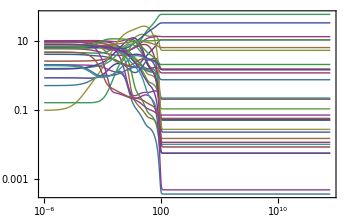

```mathematica
plotSimulation[concSol]
```

```mathematica
pfkTot=MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.ic
MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.concSol/.t->1*^5
```

PFKtot_Global→130.992

PFKtot_Global→130.992

```mathematica
unifyRateConstants[fluxSol/.t->1*^5]
```

{PFK_R_Catalysis_Bind(E->EA)→3.64824,PFK_R_Catalysis_Bind(EA->EAB)→3.64824,PFK_R_Catalysis_Transition(EAB->EPQR)→3.64824,PFK_R_Catalysis_Release(EPQR->E)→3.64824,PFK_R_Catalysis_Bind(E->EA)→0.188222,PFK_R_Catalysis_Bind(EA->EAB)→0.188222,PFK_R_Catalysis_Transition(EAB->EPQR)→0.188222,PFK_R_Catalysis_Release(EPQR->E)→0.188222,PFK_R_Catalysis_Bind(E->EA)→0.0123692,PFK_R_Catalysis_Bind(EA->EAB)→0.0123692,PFK_R_Catalysis_Transition(EAB->EPQR)→0.0123692,PFK_R_Catalysis_Release(EPQR->E)→0.0123692,PFK_R_Catalysis_Bind(E->EA)→0.0245276,PFK_R_Catalysis_Bind(EA->EAB)→0.0245276,PFK_R_Catalysis_Transition(EAB->EPQR)→0.0245276,PFK_R_Catalysis_Release(EPQR->E)→0.0245276,PFK_R_Catalysis_Bind(E->EA)→0.00395724,PFK_R_Catalysis_Bind(EA->EAB)→0.00395724,PFK_R_Catalysis_Transition(EAB->EPQR)→0.00395724,PFK_R_Catalysis_Release(EPQR->E)→0.00395724,PFK_Activation_atp→7.84287×10^-16,PFK_Activation_atp→-1.202×10^-16,PFK_Activation_atp→0.,PFK_Activation_atp→0.,PFK_Inhibition_amp→-7.63013×10^-15,PFK_Inhibition_amp→0.,PFK_Inhibition_amp→0.,PFK_Inhibition_amp→0.,PFK_TransitionStep→0.,EX_atp_c→-3.87732,EX_f6p_c→-3.87732,EX_adp_c→3.87732,EX_fdp_c→3.87732,EX_h_c→3.87732}

```mathematica
FilterRules[concSol/.t->1*^5,_enzyme]
(#[[1]]->(#[[2]]/.unifyRateConstants[rndParam]/.ssSimulConc)&/@ssEnzymeLevels/.elem_[t]:>elem)/.(MASStoolbox`MASS`parameter["PFKtot"]->Total[pfkModule["Enzymes"]]/.ic)
```

{(PFK_R^c)_^→10.5862,(PFK_R^c)_^(atp^c)→1.16958,(PFK_R^c)_^(atp^catp^c)→0.202392,(PFK_R^c)_^(atp^catp^catp^c)→0.0497914,(PFK_R^c)_^(atp^catp^catp^catp^c)→0.0226428,(PFK_R^c&atp^c)_^→0.205569,(PFK_R^c&atp^c)_^(atp^c)→0.0148607,(PFK_R^c&atp^c)_^(atp^catp^c)→0.00552044,(PFK_R^c&atp^c)_^(atp^catp^catp^c)→0.000366667,(PFK_R^c&atp^c)_^(atp^catp^catp^catp^c)→0.000485345,(PFK_R^c&atp^c&f6p^c)_^→1.51586,(PFK_R^c&atp^c&f6p^c)_^(atp^c)→0.106383,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^c)→0.010034,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^c)→0.00560987,(PFK_R^c&atp^c&f6p^c)_^(atp^catp^catp^catp^c)→0.00842705,(PFK_R^c&adp^c&fdp^c&h^c)_^→5.24143,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^c)→0.219593,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^c)→0.051485,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^c)→0.0114807,(PFK_R^c&adp^c&fdp^c&h^c)_^(atp^catp^catp^catp^c)→0.0271664,(PFK_T^c)_^→57.464,(PFK_T^c)_(amp^c)^→32.6634,(PFK_T^c)_(amp^camp^c)^→13.0566,(PFK_T^c)_(amp^camp^camp^c)^→6.30797,(PFK_T^c)_(amp^camp^camp^camp^c)^→2.0453}

{(PFK_R^c)_^→19.7468,(PFK_R^c&atp^c)_^→102.266,(PFK_R^c&atp^c&f6p^c)_^→5.05333,(PFK_R^c&adp^c&fdp^c&h^c)_^→3.92637}

```mathematica
stuff=calcPERC[catRatesFirstBranch/.ssEnzymeLevels,SteadyStateConcentrations->iABglycolysis["InitialConditions"],SteadyStateFluxes->Thread[Cases[catRatesFirstBranch,keq_Keq:>getID[keq],∞]->("PFK"/.iABglycolysis["InitialConditions"])],Parameters->param];
```

```mathematica
Solve::ratnz: "Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/Solve\", ButtonNote -> \"Solve::ratnz\"]\)"
```

```mathematica
Solve::ratnz: "Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/Solve\", ButtonNote -> \"Solve::ratnz\"]\)"
```

```mathematica
Solve::ratnz: "Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/Solve\", ButtonNote -> \"Solve::ratnz\"]\)"
```

```mathematica
General::stop: "Further output of \!\(\*StyleBox[\(Solve :: ratnz\), \"MessageName\"]\) will be suppressed during this calculation. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/General/stop\", ButtonNote -> \"General::stop\"]\)"
```

```mathematica
Simplify[stuff[[1]]]
```

```mathematica
Subscript[k, PFK_R_Catalysis_Bind(E->EA)]^⟶->(8.152941176501649*^11 Subscript[k, PFK_R_Catalysis_Bind(EA->EAB)]^⟶ Subscript[k, PFK_R_Catalysis_Release(EPQR->E)]^⟶ Subscript[k, PFK_R_Catalysis_Transition(EAB->EPQR)]^⟶)/(-6.868235294118714*^13 Subscript[k, PFK_R_Catalysis_Release(EPQR->E)]^⟶ Subscript[k, PFK_R_Catalysis_Transition(EAB->EPQR)]^⟶+Subscript[k, PFK_R_Catalysis_Bind(EA->EAB)]^⟶ (-1.304552315294118*^12 Subscript[k, PFK_R_Catalysis_Transition(EAB->EPQR)]^⟶+Subscript[k, PFK_R_Catalysis_Release(EPQR->E)]^⟶ (-8.172705882354008*^12+3.843529411764706*^7 Subscript[k, PFK_R_Catalysis_Transition(EAB->EPQR)]^⟶)))
```